```mathematica
plotBuffer[path_]:=Module[{file,headings,points},
file=Import[path];
headings=file//First;
points=file//Rest;
data=Most[points]//Transpose;
Print[Join[{headings},Take[points,-10]]//TableForm];
ListLinePlot[
data,
PlotLegends->headings
]
]
```

```mathematica
plotBuffer["D:\\measureBuffer\\countCells.csv"]
```

nPellets | nBuffer | nEnergy | nCells
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22616 | 71804 | 5580 | 0

-Graphics-

nPellets | nBuffer | nEnergy | nCells
534 | 24251 | 72000 | 3215
534 | 24251 | 72000 | 3215
534 | 24251 | 72000 | 3215
534 | 24251 | 72000 | 3215
534 | 24251 | 72000 | 3215
534 | 24251 | 72000 | 3215
535 | 24251 | 72000 | 3214
535 | 24251 | 72000 | 3214
535 | 24251 | 72000 | 3214
535 |  |  |

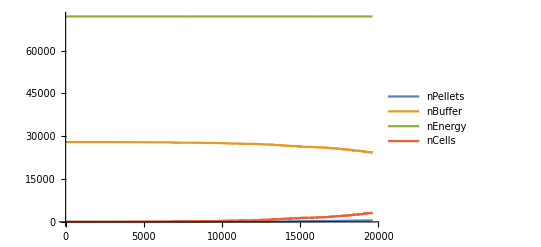

```mathematica
plotBuffer["D:\\measureBuffer 2\\countCells.csv"]
```